```mathematica
Clear["Global`*"]
```

## Modules

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/future_brr_new/";*)
```

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_Tiingo/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_Tiingo_LTC/";
```

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=Module[{v},
v=Catch[CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x], _SystemException];
If[NumberQ[v],v,0]
]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

Empirical DF (values lie strictly in [0,1])

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Clear[obj]
```

```mathematica
(* note that const needs to be defined outside *)
obj[α_?NumericQ,β_?NumericQ, target_]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β];
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}];
Sqrt[Total[(target-f)^2]]
]
```

```mathematica
calibrate[data_]:=calibrate[data, 0.5,0]
```

```mathematica
calibrate[data_,α0_,β0_]:=Module[{q,target,f,α,β,δ,q0,F1,t,sol},
target=Table[QDemp[q,data⟦;;,1⟧,data⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}];
(*Print[target];*)
t=Timing[sol=NMinimize[{obj[α,β,target],α>0 &&Abs[β]<α}, {{α,Max[α0-0.5,0],α0+0.5},{β,β0-0.1,β0+0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1(*,EvaluationMonitor:>Print["α = " <> ToString[α] <> ", β = " <>  ToString[β] <> ", val = " <> ToString[obj[α,β,target]]]*)]];
(*Print[t];*)
(*Print["[calibrate] α, β: " <> ToString[{α,β}]];*)
{α/.sol⟦2⟧,β/.sol⟦2⟧,sol⟦1⟧,t⟦1⟧}
]
```

```mathematica
InSampeCalibrateAndSimulate[data_]:=InSampeCalibrateAndSimulate[data,0.5,0]
```

```mathematica
InSampeCalibrateAndSimulate[data_, α0_,β0_]:=Module[{hatqd, target, sol,α,β,δ,μ, μ1,μ2, δ1,δ2,γ,μIG, μ1IG, μ2IG,λ, λ1, λ2, Y, W, W1, W2, Z, Z1, Z2, X1, X2, usim, vsim},
hatqd=Table[QDemp[q,data⟦1;;All,1⟧,data⟦1;;All,2⟧],{q,{0.05,0.1,0.9,0.95}}];
target=Flatten[Join[{SpearmanRho[data⟦1;;All,1⟧,data⟦1;;All,2⟧]},hatqd]];
const=Sin[1/6 target⟦1⟧ π] 2;
sol=calibrate[data,α0,β0];
α=sol⟦1⟧; 
β=sol⟦2⟧;
δ=const δs[α,β];
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
usim = hatF[X1];
vsim = hatF[X2];
{α,β,δ, usim, vsim}
]
```

```mathematica
Clear[r]
r[h_?NumericQ]:=rs -h rf;
```

```mathematica
Clear[ES]
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
Clear[f, SpectralRisk];
f[s_, p_?NumericQ, k_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p];
SpectralRisk[h_?NumericQ, k_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p,k], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
RiskMeasures[rbtc_, rbrr_,usim_, vsim_]:=Module[{dbtc, dbrr,h, hvar,hVaR99, hVaR95, hES99, hES95,hSR10, hSR20,sol,solutions},
dbrr=EmpiricalDistribution[rbrr];
dbtc=EmpiricalDistribution[rbtc];
rs=InverseCDF[dbrr, usim];
rf=InverseCDF[dbtc, vsim];
solutions={};
Print["Variance"];
(*sol=NMinimize[Variance[r[h]], h];*)
hvar=Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf];
Print["VaR 99"];
sol=NMinimize[-Quantile[r[h],0.01], h];
AppendTo[solutions,sol];
hVaR99 = h/.sol[[2]];
Print["VaR 95"];
sol=NMinimize[-Quantile[r[h],0.05], h];
AppendTo[solutions,sol];
hVaR95 = h/.sol[[2]];
Print["ES 99"];
sol = NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES99 = h/.sol[[2]];
Print["ES 95"];
sol=NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES95 = h/.sol[[2]];
Print["Spectral 10"];
sol=NMinimize[SpectralRisk[h,10],h];
AppendTo[solutions,sol];
hSR10 = h/.sol[[2]];
(*Print["Spectral 20"];*)
(*sol=NMinimize[SpectralRisk[h,20],h];
AppendTo[solutions,sol];
hSR20 = h/.sol[[2]];*)
{hvar, hVaR99, hVaR95, hES99, hES95, hSR10, solutions}
]
```

```mathematica
HedgeEffectiveness[h_] := Module[{v},
v={};
AppendTo[v,1-Variance[r[h⟦1⟧]]/Variance[rs]];
AppendTo[v,1-Quantile[r[h⟦2⟧],0.01]/Quantile[rs, 0.01]];
AppendTo[v, 1-Quantile[r[h⟦3⟧],0.05]/Quantile[rs, 0.05]];
AppendTo[v,1-ES[h⟦4⟧,0.99]/ES[0,0.99]];
AppendTo[v,1-ES[h⟦5⟧,0.95]/ES[0,0.95]];
AppendTo[v,1-SpectralRisk[h⟦6⟧,10]/SpectralRisk[0,10]];
v
]
```

## Run modules

```mathematica
SeedRandom[123456];
n=50000;
```

```mathematica
heInsample={};
heOutsample={};
```

```mathematica
(*kk=0;
data = 
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[kk] <> ".csv"];*)
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

CAREFUL: spot and future are the other way round in BRR data set

```mathematica
(*data[[1;;10]]*)
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
5 | 2021-01-27 | 31038.2 | 31905. | -0.0310281 | -0.0204754
6 | 2021-01-26 | 32016.3 | 32565. | -0.0128355 | -0.0492799
7 | 2021-01-25 | 32429.9 | 34210. | -0.0323413 | -0.00160643
8 | 2021-01-22 | 33495.9 | 34265. | 0.0683149 | 0.0507328
9 | 2021-01-21 | 31284. | 32570. | -0.110154 | -0.0966491
10 | 2021-01-20 | 34927.1 | 35875. | -0.041842 | -0.0462983
11 | 2021-01-19 | 36419.5 | 37575. | 0.0068495 | 0.0280682
12 | 2021-01-15 | 36170.9 | 36535. | -0.0686241 | -0.103525
13 | 2021-01-14 | 38740.2 | 40520. | 0.0316585 | 0.0819984)

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | ltc Price | log return future | log return ltc
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 210.069 | 0.0212907 | 0.0373946
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 202.358 | -0.0904653 | -0.375913
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 294.698 | -0.0196938 | 0.0455332
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 281.581 | -0.131645 | -0.139733
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 323.809 | 0.03685 | 0.0859344
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 297.144 | -0.119603 | -0.177521
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 354.866 | -0.042369 | -0.0471009
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 371.98 | 0.018947 | 0.0151204
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 366.398 | -0.0359909 | 0.0584074)

```mathematica
StringSplit[data[[2,2]]][[1]]
```

2021-05-20

```mathematica
data[[1,7]]
```

log return ltc

```mathematica
data[[1,6]]
```

log return future

```mathematica
α0=0.5; β0=0;
```

```mathematica
For[kk=39, kk≥0, kk--,
Print[kk];
SeedRandom[123456];
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;
{α,β,δ,usim,vsim}=InSampeCalibrateAndSimulate[data⟦2;;All,6;;7⟧];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv", {DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}],α,β,δ}];Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv", {usim, vsim}ᵀ];
α0=α; β0=β;
]
```

39

38

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: 1.25331/(1.09180814843873×10^345) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NMinimize::nnum: The function value √((0.6-20. F2NIG2(InverseCDF[HyperbolicDistribution[«5»],0.05],«6»,InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}]))^2+(0.633333-10. F2NIG2(«1»))^2+(«1»)^2+(0.266667-20. (-0.9+F2NIG2(InverseCDF[«2»],«6»,«1»)))^2) is not a number at {α$382949759,β$382949759} = {28.2964,2.18771}.

37

NMinimize::nnum: The function value √((0.6-20. F2NIG2(InverseCDF[HyperbolicDistribution[«5»],0.05],«6»,InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}]))^2+(0.633333-10. F2NIG2(«1»))^2+(«1»)^2+(0.333333-20. (-0.9+F2NIG2(InverseCDF[«2»],«6»,«1»)))^2) is not a number at {α$383395584,β$383395584} = {28.2964,2.18771}.

36

35

34

33

32

31

30

29

28

27

26

25

24

23

22

21

20

19

18

17

16

15

14

13

12

11

10

9

8

7

6

5

4

3

2

1

0

```mathematica
{α0,β0}
```

{2.37993,-1.4806}

```mathematica
dataDirectory
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../processed_data/BBT_future_Tiingo_LTC/

```mathematica
For[kk=0, kk≤111, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
data2= Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,6⟧;
rbrr=data⟦2;;All,7⟧;
{dates2,α,β,δ}=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv" ];utmp = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv"];usim=utmp⟦1;;All,1⟧;
vsim=utmp⟦1;;All,2⟧;
Print["Risk Measures..."];
h=RiskMeasures[rbtc, rbrr, usim, vsim];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv", Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]}, h]];
he=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]]; (* in-sample *)
AppendTo[heInsample, he];
(* out-of-sample *)
rs=data2⟦2;;All,7⟧;
rf=data2⟦2;;All,6⟧;
he2=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]];
AppendTo[heOutsample, he2];
]
```

0

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.989497694257557}. NIntegrate obtained 0.0979153 and 0.000106292 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

1

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.989497694257557}. NIntegrate obtained 0.0973492 and 0.000130588 for the integral and error estimates.

2

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.989497694257557}. NIntegrate obtained 0.0973117 and 0.000138821 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

3

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

4

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

5

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

6

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

7

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

8

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

9

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

10

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

11

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

12

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

13

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

14

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

15

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

16

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

17

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

18

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

19

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

20

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

21

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

22

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

23

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

24

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

25

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

26

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

27

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

28

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

29

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

30

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

31

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

32

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

33

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

34

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

35

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

36

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

37

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

38

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

39

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

40

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

41

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

42

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

43

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

44

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

45

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

46

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

47

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

48

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

49

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

50

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

51

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

52

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

53

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

54

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

55

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

56

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

57

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

58

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

59

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

60

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

61

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

62

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

63

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

64

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

65

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

66

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

67

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

68

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

69

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

70

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

71

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

72

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

73

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

74

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

75

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

76

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

77

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

78

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

79

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

80

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

81

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

82

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

83

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

84

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

85

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

86

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

87

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

88

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

89

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

90

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

91

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

92

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

93

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

94

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

95

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

96

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

97

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

98

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

99

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

100

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

101

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

102

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

103

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

104

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

105

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

106

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

107

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

108

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

109

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

110

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

111

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

## Hedge effectiveness

```mathematica
t1=TableForm[heInsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.568077 | 0.298646 | 0.358668 | 0.271537 | 0.330673 | 0.39208
 | 2021-05-13 | 0.586436 | 0.483302 | 0.381562 | 0.322527 | 0.381224 | 0.375342
 | 2021-05-06 | 0.578647 | 0.497413 | 0.363217 | 0.336588 | 0.371172 | 0.367671
 | 2021-04-29 | 0.60255 | 0.49386 | 0.376046 | 0.346588 | 0.381006 | 0.406082
 | 2021-04-22 | 0.602255 | 0.501847 | 0.380844 | 0.345793 | 0.381378 | 0.40259
 | 2021-04-15 | 0.628069 | 0.515208 | 0.37469 | 0.360189 | 0.388921 | 0.433286
 | 2021-04-08 | 0.628819 | 0.522092 | 0.384045 | 0.364962 | 0.395344 | 0.429408
 | 2021-04-01 | 0.646969 | 0.552295 | 0.411188 | 0.380579 | 0.414387 | 0.449125
 | 2021-03-25 | 0.628986 | 0.52655 | 0.380096 | 0.377153 | 0.397146 | 0.423792
 | 2021-03-18 | 0.625452 | 0.521896 | 0.392745 | 0.367937 | 0.397595 | 0.422679
 | 2021-03-11 | 0.665403 | 0.542512 | 0.408435 | 0.388522 | 0.419782 | 0.471723
 | 2021-03-04 | 0.6547 | 0.539033 | 0.399223 | 0.389157 | 0.415282 | 0.453124
 | 2021-02-25 | 0.671431 | 0.551009 | 0.398175 | 0.396077 | 0.423046 | 0.474627
 | 2021-02-18 | 0.66571 | 0.586783 | 0.394671 | 0.422197 | 0.408268 | 0.470375
 | 2021-02-10 | 0.651596 | 0.578132 | 0.396608 | 0.411927 | 0.40185 | 0.455444
 | 2021-02-03 | 0.680718 | 0.594331 | 0.408671 | 0.428542 | 0.42382 | 0.481832
 | 2021-01-27 | 0.677987 | 0.594755 | 0.442507 | 0.430358 | 0.425333 | 0.471065
 | 2021-01-20 | 0.664655 | 0.595096 | 0.424235 | 0.422714 | 0.417688 | 0.466025
 | 2021-01-12 | 0.658576 | 0.585561 | 0.392637 | 0.413909 | 0.404954 | 0.468257
 | 2021-01-05 | 0.647036 | 0.472909 | 0.432071 | 0.401947 | 0.388899 | 0.467768
 | 2020-12-28 | 0.655142 | 0.482759 | 0.421682 | 0.402677 | 0.394115 | 0.465961
 | 2020-12-18 | 0.656879 | 0.491955 | 0.442741 | 0.410492 | 0.410616 | 0.453382
 | 2020-12-11 | 0.663949 | 0.503841 | 0.462887 | 0.426882 | 0.423014 | 0.453394
 | 2020-12-04 | 0.65862 | 0.494628 | 0.455674 | 0.416807 | 0.411543 | 0.455164
 | 2020-11-27 | 0.656593 | 0.527629 | 0.498614 | 0.415799 | 0.446009 | 0.420403
 | 2020-11-19 | 0.643158 | 0.533318 | 0.454213 | 0.420972 | 0.421733 | 0.415764
 | 2020-11-12 | 0.616974 | 0.518835 | 0.454426 | 0.412382 | 0.412736 | 0.38213
 | 2020-11-05 | 0.609883 | 0.512324 | 0.442779 | 0.409016 | 0.401622 | 0.378156
 | 2020-10-29 | 0.629327 | 0.518809 | 0.465629 | 0.411675 | 0.408038 | 0.404598
 | 2020-10-22 | 0.630274 | 0.516861 | 0.474054 | 0.409944 | 0.41019 | 0.406572
 | 2020-10-15 | 0.611281 | 0.510232 | 0.483934 | 0.411338 | 0.403923 | 0.370807
 | 2020-10-08 | 0.600657 | 0.483097 | 0.450687 | 0.394868 | 0.371772 | 0.386784
 | 2020-10-01 | 0.607787 | 0.503685 | 0.440638 | 0.397595 | 0.386709 | 0.383655
 | 2020-09-24 | 0.601869 | 0.490473 | 0.420527 | 0.386729 | 0.373515 | 0.384932
 | 2020-09-17 | 0.61067 | 0.484812 | 0.432548 | 0.3876 | 0.396296 | 0.378818
 | 2020-09-10 | 0.603741 | 0.476772 | 0.451209 | 0.391081 | 0.393803 | 0.360162
 | 2020-09-02 | 0.591167 | 0.475864 | 0.401614 | 0.411691 | 0.401218 | 0.340342
 | 2020-08-26 | 0.538598 | 0.438355 | 0.347323 | 0.389273 | 0.345756 | 0.341317
 | 2020-08-19 | 0.520114 | 0.422387 | 0.33568 | 0.374664 | 0.330422 | 0.333164
 | 2020-08-12 | 0.526243 | 0.423782 | 0.391137 | 0.330924 | 0.343072 | 0.314429
 | 2020-08-05 | 0.530701 | 0.418658 | 0.356717 | 0.340216 | 0.337837 | 0.32658
 | 2020-07-29 | 0.524966 | 0.422062 | 0.376277 | 0.345144 | 0.343729 | 0.301802
 | 2020-07-22 | 0.521307 | 0.422233 | 0.328783 | 0.385788 | 0.33948 | 0.323494
 | 2020-07-15 | 0.520808 | 0.411836 | 0.319426 | 0.365147 | 0.325909 | 0.330976
 | 2020-07-08 | 0.522993 | 0.407377 | 0.316472 | 0.347961 | 0.321276 | 0.329349
 | 2020-06-30 | 0.504321 | 0.402155 | 0.300959 | 0.352912 | 0.313316 | 0.31932
 | 2020-06-23 | 0.494155 | 0.391557 | 0.28928 | 0.344223 | 0.304328 | 0.315168
 | 2020-06-16 | 0.499387 | 0.387984 | 0.286064 | 0.347459 | 0.310036 | 0.319366
 | 2020-06-09 | 0.536956 | 0.384231 | 0.393777 | 0.318691 | 0.335742 | 0.338054
 | 2020-06-02 | 0.538171 | 0.384681 | 0.393777 | 0.31872 | 0.336095 | 0.3387
 | 2020-05-26 | 0.535875 | 0.377296 | 0.396184 | 0.316008 | 0.332817 | 0.336597
 | 2020-05-18 | 0.496472 | 0.364067 | 0.391348 | 0.304757 | 0.318559 | 0.293092
 | 2020-05-11 | 0.507385 | 0.36256 | 0.339259 | 0.316465 | 0.310433 | 0.318451
 | 2020-05-04 | 0.495342 | 0.374174 | 0.324634 | 0.310953 | 0.311685 | 0.29564
 | 2020-04-27 | 0.521346 | 0.385888 | 0.31713 | 0.309632 | 0.317147 | 0.324579
 | 2020-04-20 | 0.522329 | 0.38678 | 0.33563 | 0.313872 | 0.322539 | 0.31949
 | 2020-04-13 | 0.515732 | 0.380252 | 0.32508 | 0.309856 | 0.317646 | 0.312706
 | 2020-04-03 | 0.50406 | 0.384019 | 0.297926 | 0.307977 | 0.304819 | 0.314591
 | 2020-03-27 | 0.496068 | 0.379462 | 0.301694 | 0.297216 | 0.301403 | 0.297871
 | 2020-03-20 | 0.49643 | 0.375227 | 0.303972 | 0.298909 | 0.301888 | 0.308596
 | 2020-03-13 | 0.478364 | 0.365998 | 0.299063 | 0.287523 | 0.299717 | 0.281398
 | 2020-03-06 | 0.47832 | 0.259472 | 0.349273 | 0.171072 | 0.280985 | 0.305327
 | 2020-02-28 | 0.478919 | 0.243213 | 0.358986 | 0.15942 | 0.281022 | 0.304523
 | 2020-02-21 | 0.504783 | 0.266921 | 0.34248 | 0.188023 | 0.286637 | 0.330906
 | 2020-02-13 | 0.510296 | 0.259395 | 0.3344 | 0.188192 | 0.291588 | 0.334593
 | 2020-02-06 | 0.500133 | 0.263922 | 0.348569 | 0.180165 | 0.290812 | 0.326379
 | 2020-01-30 | 0.510178 | 0.264685 | 0.360149 | 0.193268 | 0.302816 | 0.319673
 | 2020-01-23 | 0.512528 | 0.283035 | 0.371474 | 0.198763 | 0.327046 | 0.308899
 | 2020-01-15 | 0.497449 | 0.273542 | 0.37557 | 0.181596 | 0.31891 | 0.300835
 | 2020-01-08 | 0.497694 | 0.270243 | 0.369082 | 0.184672 | 0.317374 | 0.300019
 | 2019-12-31 | 0.510925 | 0.260338 | 0.347761 | 0.183786 | 0.303917 | 0.318552
 | 2019-12-23 | 0.509866 | 0.248426 | 0.346554 | 0.185863 | 0.297323 | 0.329968
 | 2019-12-16 | 0.508343 | 0.247259 | 0.379084 | 0.185483 | 0.297485 | 0.325322
 | 2019-12-09 | 0.505809 | 0.259799 | 0.355946 | 0.188447 | 0.307442 | 0.316528
 | 2019-12-02 | 0.510476 | 0.260105 | 0.347526 | 0.184447 | 0.306613 | 0.318131
 | 2019-11-22 | 0.508901 | 0.251648 | 0.351881 | 0.181641 | 0.305361 | 0.318716
 | 2019-11-15 | 0.508974 | 0.258404 | 0.378594 | 0.190642 | 0.308414 | 0.305237
 | 2019-11-08 | 0.504083 | 0.257408 | 0.403796 | 0.18828 | 0.321866 | 0.303401
 | 2019-11-01 | 0.530446 | 0.259288 | 0.369553 | 0.204291 | 0.31103 | 0.337712
 | 2019-10-25 | 0.511126 | 0.259282 | 0.409146 | 0.190092 | 0.325798 | 0.308181
 | 2019-10-18 | 0.510681 | 0.258497 | 0.40287 | 0.195614 | 0.325496 | 0.304369
 | 2019-10-11 | 0.535497 | 0.252899 | 0.432242 | 0.193807 | 0.322178 | 0.334689
 | 2019-10-04 | 0.53162 | 0.249974 | 0.429395 | 0.189659 | 0.311411 | 0.337333
 | 2019-09-27 | 0.536156 | 0.256646 | 0.430987 | 0.193445 | 0.323655 | 0.335041
 | 2019-09-20 | 0.50028 | 0.266394 | 0.387449 | 0.1665 | 0.306571 | 0.307356
 | 2019-09-13 | 0.537633 | 0.277247 | 0.385959 | 0.177499 | 0.317423 | 0.345459
 | 2019-09-06 | 0.52507 | 0.285898 | 0.384286 | 0.19542 | 0.320871 | 0.327674
 | 2019-08-29 | 0.538998 | 0.272743 | 0.450323 | 0.173336 | 0.326351 | 0.338114
 | 2019-08-22 | 0.526419 | 0.266739 | 0.449168 | 0.168715 | 0.322751 | 0.328209
 | 2019-08-15 | 0.565948 | 0.274228 | 0.473457 | 0.176673 | 0.331202 | 0.365575
 | 2019-08-08 | 0.553397 | 0.284615 | 0.486691 | 0.178957 | 0.342388 | 0.348079
 | 2019-08-01 | 0.585363 | 0.286799 | 0.502046 | 0.183714 | 0.355948 | 0.373676
 | 2019-07-25 | 0.589508 | 0.284283 | 0.483241 | 0.188074 | 0.337195 | 0.38988
 | 2019-07-18 | 0.605648 | 0.303009 | 0.492565 | 0.199492 | 0.352226 | 0.399325
 | 2019-07-11 | 0.59106 | 0.326557 | 0.430961 | 0.218242 | 0.347369 | 0.386057
 | 2019-07-03 | 0.593384 | 0.324578 | 0.448252 | 0.211902 | 0.351816 | 0.38836
 | 2019-06-26 | 0.604773 | 0.326254 | 0.441208 | 0.218391 | 0.340329 | 0.417046
 | 2019-06-19 | 0.629811 | 0.352481 | 0.460623 | 0.243689 | 0.366455 | 0.420325
 | 2019-06-12 | 0.641356 | 0.360547 | 0.474273 | 0.250299 | 0.372878 | 0.430724
 | 2019-06-05 | 0.663509 | 0.372898 | 0.535753 | 0.256203 | 0.394465 | 0.447072
 | 2019-05-29 | 0.663661 | 0.368581 | 0.533915 | 0.254099 | 0.392124 | 0.450163
 | 2019-05-21 | 0.666439 | 0.374444 | 0.517119 | 0.263294 | 0.391085 | 0.450502
 | 2019-05-14 | 0.635852 | 0.339839 | 0.534145 | 0.226844 | 0.372131 | 0.425858
 | 2019-05-07 | 0.635258 | 0.351101 | 0.535394 | 0.238066 | 0.38419 | 0.404373
 | 2019-04-30 | 0.639007 | 0.332621 | 0.537777 | 0.232602 | 0.378301 | 0.406663
 | 2019-04-23 | 0.65899 | 0.356304 | 0.536154 | 0.252094 | 0.393084 | 0.429826
 | 2019-04-15 | 0.679585 | 0.389437 | 0.550384 | 0.2806 | 0.424116 | 0.439621
 | 2019-04-08 | 0.658753 | 0.378695 | 0.526914 | 0.284353 | 0.407872 | 0.406062
 | 2019-04-01 | 0.653712 | 0.363586 | 0.519997 | 0.290513 | 0.408864 | 0.393187
 | 2019-03-25 | 0.661456 | 0.402161 | 0.532141 | 0.389966 | 0.445733 | 0.381339
 | 2019-03-18 | 0.642106 | 0.397501 | 0.509234 | 0.395912 | 0.431633 | 0.367849
 | 2019-03-11 | 0.647616 | 0.399724 | 0.503757 | 0.401007 | 0.432463 | 0.379121

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.csv", Prepend[heInsample,{"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"}]];
```

```mathematica
TableForm[heOutsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.702025 | 0.525827 | 0.6072 | 0.5691 | 0.600864 | 0.310503
 | 2021-05-13 | 0.444606 | 0.226112 | 0.245379 | 0.22395 | 0.242888 | 0.211665
 | 2021-05-06 | 0.663716 | 0.542794 | 0.680589 | 0.611813 | 0.657097 | -0.581272
 | 2021-04-29 | 0.192967 | 0.287968 | 0.264255 | 0.286281 | 0.284639 | 0.295128
 | 2021-04-22 | 0.433566 | 0.354495 | 0.324433 | 0.343255 | 0.337504 | 0.243613
 | 2021-04-15 | 0.520377 | 0.690909 | 0.705199 | 0.72851 | 0.712338 | -0.44902
 | 2021-04-08 | 0.689283 | 0.366403 | 0.329091 | 0.399025 | 0.360213 | 0.415692
 | 2021-04-01 | 0.151021 | 0.493452 | 0.607463 | 0.532258 | 0.582673 | -0.220995
 | 2021-03-25 | 0.562926 | 0.240462 | 0.249962 | 0.285571 | 0.287433 | 0.520604
 | 2021-03-18 | 0.582206 | 0.678527 | 0.668606 | 0.637098 | 0.666324 | -2.88689
 | 2021-03-11 | -0.0821314 | 0.0517687 | 0.053434 | 0.0517635 | 0.0529413 | -0.158678
 | 2021-03-04 | 0.594114 | 9.19537 | 9.3211 | 9.19537 | 9.17324 | 1.00844
 | 2021-02-25 | 0.662761 | 0.436753 | 0.404066 | 0.449204 | 0.455065 | 0.595966
 | 2021-02-18 | 0.643714 | 0.341251 | 0.344294 | 0.354607 | 0.346154 | -0.0368962
 | 2021-02-10 | 0.644187 | 0.168291 | -0.324066 | 0.13979 | -0.195479 | 0.631624
 | 2021-02-03 | -1.00309 | -0.883592 | -0.920573 | -1.31213 | -1.23051 | 0.100483
 | 2021-01-27 | 0.567255 | -0.175765 | -0.231624 | -0.502824 | -0.441223 | 0.705746
 | 2021-01-20 | 0.923213 | 0.700474 | 0.707718 | 0.696511 | 0.717475 | 0.509761
 | 2021-01-12 | 0.648821 | 0.55507 | 0.558224 | 0.578093 | 0.544521 | 0.261355
 | 2021-01-05 | 0.899945 | 0.58256 | 0.685406 | 0.569043 | 0.620113 | 0.610865
 | 2020-12-28 | 0.489227 | -0.488308 | -0.797703 | -0.479715 | -0.58808 | 0.542087
 | 2020-12-18 | 0.81633 | 0.0506855 | 0.0560127 | 0.0502787 | 0.0530112 | 0.80052
 | 2020-12-11 | 0.689103 | 1.75789 | 2.02309 | 1.72269 | 1.83085 | 0.57562
 | 2020-12-04 | 0.320014 | 0.249162 | 0.287952 | 0.245369 | 0.264406 | 2.15661
 | 2020-11-27 | 0.871297 | 0.448208 | 0.497069 | 0.430132 | 0.480622 | 0.717218
 | 2020-11-19 | 0.71784 | 0.586809 | 0.644374 | 0.586809 | 0.624532 | -0.146925
 | 2020-11-12 | 0.0760218 | 0.123658 | 0.129175 | 0.118782 | 0.128659 | 0.178899
 | 2020-11-05 | 0.575115 | -0.0954623 | -0.132632 | -0.0639852 | -0.128883 | 0.63632
 | 2020-10-29 | 0.906897 | -0.226568 | -0.238004 | -0.226501 | -0.238651 | 0.95128
 | 2020-10-22 | -0.209657 | 0.00335153 | -0.0810434 | 0.00824254 | -0.0266068 | -0.206018
 | 2020-10-15 | 0.598552 | -0.0165448 | -0.0459261 | -0.00173387 | -0.0344894 | 0.519576
 | 2020-10-08 | 0.804961 | 0.535788 | 0.548132 | 0.516666 | 0.576049 | 0.604648
 | 2020-10-01 | 0.384526 | 0.260205 | 0.28243 | 0.259244 | 0.272258 | 0.165703
 | 2020-09-24 | 0.321978 | 0.434687 | 0.389542 | 0.397123 | 0.404584 | 0.282232
 | 2020-09-17 | 0.664363 | 0.349233 | 0.381487 | 0.352427 | 0.37562 | 0.710443
 | 2020-09-10 | -3.1668 | -1.18233 | -1.2687 | -1.13562 | -1.26437 | -0.273261
 | 2020-09-02 | 0.825942 | 0.444544 | 0.432137 | 0.450021 | 0.448459 | 0.739823
 | 2020-08-26 | 0.616144 | 0.508521 | 0.453832 | 0.62337 | 0.545154 | 0.216991
 | 2020-08-19 | 0.619783 | 0.555393 | 0.478541 | 0.642331 | 0.557226 | 0.266174
 | 2020-08-12 | 0.426547 | 0.192019 | 0.205343 | 0.191818 | 0.208603 | 0.215361
 | 2020-08-05 | 0.86861 | 0.448563 | 0.462469 | 0.449628 | 0.423792 | 0.878594
 | 2020-07-29 | 0.52985 | 0.44919 | 0.429456 | 0.412052 | 0.443971 | 0.152021
 | 2020-07-22 | 0.657038 | -0.870019 | -0.729839 | -1.0011 | -0.877253 | 0.544286
 | 2020-07-15 | 0.488628 | 0.151522 | 0.142696 | 0.185786 | 0.16853 | 0.370637
 | 2020-07-08 | 0.598961 | 0.361936 | 0.361936 | 0.361936 | 0.361936 | 0.259623
 | 2020-06-30 | 0.719043 | 1.01138 | 1.03175 | 0.879557 | 0.947062 | 0.354725
 | 2020-06-23 | 0.273353 | 0.12629 | 0.120788 | 0.135641 | 0.129458 | -0.329011
 | 2020-06-16 | 0.815419 | 0.190698 | 0.212472 | 0.0818589 | 0.147203 | 0.696307
 | 2020-06-09 | 0.854087 | 0.681167 | 0.684335 | 0.655332 | 0.681835 | 0.559178
 | 2020-06-02 | 0.138216 | 0.100245 | 0.117003 | 0.0883251 | 0.103464 | 0.23701
 | 2020-05-26 | 0.445905 | 0.212221 | 0.216819 | 0.189344 | 0.219975 | 0.344796
 | 2020-05-18 | 0.752955 | 0.658176 | 0.742316 | 0.651242 | 0.715292 | 0.178188
 | 2020-05-11 | 0.638378 | 0.347699 | 0.306331 | 0.341638 | 0.198339 | 0.597446
 | 2020-05-04 | 0.955012 | 0.720303 | 0.715478 | 0.642024 | 0.706124 | 1.11623
 | 2020-04-27 | 0.711748 | -0.258887 | -0.285896 | -0.239691 | -0.261017 | 0.793598
 | 2020-04-20 | -0.709633 | -1.14661 | -1.34914 | -1.02406 | -1.18804 | 0.193831
 | 2020-04-13 | 0.89608 | 0.498499 | 0.586712 | 0.4455 | 0.517723 | 0.878982
 | 2020-04-03 | 0.798253 | 0.469767 | 0.551244 | 0.463426 | 0.501548 | 0.682961
 | 2020-03-27 | 0.875034 | 0.665641 | 0.394337 | 0.813167 | 0.62525 | 0.725059
 | 2020-03-20 | 0.811592 | 0.293289 | 0.348389 | 0.269128 | 0.310238 | 0.741612
 | 2020-03-13 | 0.960224 | 0.518766 | 0.618992 | 0.509958 | 0.576092 | 1.06277
 | 2020-03-06 | 0.620463 | 0.426632 | 0.639187 | 0.410194 | 0.567137 | -2.20206
 | 2020-02-28 | 0.882749 | 0.254901 | 0.286024 | 0.236526 | 0.269177 | 0.725155
 | 2020-02-21 | 0.523342 | 0.257233 | 0.377078 | 0.231314 | 0.319742 | -0.303889
 | 2020-02-13 | 0.635056 | 0.397069 | 0.50466 | 0.320688 | 0.431156 | 0.235756
 | 2020-02-06 | 0.479488 | 0.75279 | 0.867829 | 0.634321 | 0.913042 | 0.271248
 | 2020-01-30 | 0.742981 | 0.235666 | 0.382573 | 0.237379 | 0.307509 | 0.511935
 | 2020-01-23 | 0.0932218 | -1.03781 | -1.44236 | -0.859665 | -1.19249 | 0.194162
 | 2020-01-15 | 0.555033 | 0.2562 | 0.379129 | 0.205744 | 0.31028 | 0.326914
 | 2020-01-08 | 0.664963 | 1.40617 | 1.04894 | 1.26288 | 1.24832 | 0.464333
 | 2019-12-31 | 0.599786 | 0.338096 | 0.202441 | 0.332125 | 0.39741 | 0.434151
 | 2019-12-23 | 0.535292 | 0.268062 | 0.420511 | 0.222148 | 0.331392 | 0.0873794
 | 2019-12-16 | 0.833284 | 0.23606 | 0.436178 | 0.23606 | 0.351013 | 0.854757
 | 2019-12-09 | 0.715586 | 0.336025 | 0.433818 | 0.257864 | 0.366749 | 0.552298
 | 2019-12-02 | -1.75552 | -0.28813 | -0.701414 | -0.215709 | -0.521546 | -0.390639
 | 2019-11-22 | 0.766999 | 0.390754 | 0.606508 | 0.373122 | 0.505516 | 0.24889
 | 2019-11-15 | 0.828419 | 0.465688 | 0.632729 | 0.402663 | 0.54806 | -1.50602
 | 2019-11-08 | -0.0392747 | 0.353694 | 0.40109 | 0.266449 | 0.366521 | -0.3918
 | 2019-11-01 | 0.659816 | 0.38566 | 0.453386 | 0.302413 | 0.378851 | 0.421798
 | 2019-10-25 | -2.3679 | -0.468394 | -1.99935 | -0.0633675 | -1.24436 | 0.0076608
 | 2019-10-18 | 0.97618 | 0.566159 | 0.861367 | 0.522559 | 0.728553 | 0.874224
 | 2019-10-11 | 0.684009 | 0.320921 | 0.476121 | 0.272996 | 0.394299 | 0.327986
 | 2019-10-04 | 0.897222 | 0.449192 | 0.483063 | 0.39386 | 0.458093 | 0.842079
 | 2019-09-27 | -0.753867 | -0.0672959 | -0.976818 | -0.0563215 | -0.590661 | 0.152349
 | 2019-09-20 | 0.871504 | 0.544839 | 0.672923 | 0.413681 | 0.579159 | -2.84361
 | 2019-09-13 | -0.00529265 | -0.0907939 | -0.116329 | -0.0720094 | -0.0947673 | 0.132685
 | 2019-09-06 | -0.600646 | -0.166922 | -0.191252 | -0.138635 | -0.17173 | -0.213489
 | 2019-08-29 | 0.686255 | 0.242411 | 0.335064 | 0.173911 | 0.277453 | 0.658734
 | 2019-08-22 | 0.844053 | 0.335962 | 0.494473 | 0.269188 | 0.419076 | 1.22934
 | 2019-08-15 | -4.43735 | -0.351555 | -0.928445 | -0.190677 | -0.654228 | -3.21122
 | 2019-08-08 | -0.348968 | 0.197343 | 0.123646 | 0.228745 | 0.159668 | -2.2055
 | 2019-08-01 | 0.311673 | -0.178504 | -0.245484 | -0.134293 | -0.210187 | 0.750173
 | 2019-07-25 | 0.761012 | 0.731182 | 0.652352 | 0.524164 | 0.784464 | 0.54929
 | 2019-07-18 | -1.68907 | 0.141644 | 0.206828 | 0.115196 | 0.177712 | -13.2789
 | 2019-07-11 | 0.744197 | 0.41914 | 0.486458 | 0.320376 | 0.426359 | 0.178979
 | 2019-07-03 | 0.425284 | 0.305408 | 0.15899 | 0.2393 | 0.335187 | 0.845266
 | 2019-06-26 | -1.44293 | 0.604984 | 0.322925 | 0.7584 | 0.529656 | -4.2559
 | 2019-06-19 | -7.5563 | -3.5109 | -5.0777 | -2.18198 | -3.47979 | 2.65127
 | 2019-06-12 | -1.44805 | -0.169452 | -0.939261 | -0.140984 | -0.265753 | -0.160937
 | 2019-06-05 | -0.0891128 | -10.0166 | -15.212 | -8.44246 | -12.2404 | 0.181834
 | 2019-05-29 | 0.853501 | 0.757509 | 0.788631 | 0.698237 | 0.770113 | -0.369043
 | 2019-05-21 | 0.745615 | 0.558724 | 0.764396 | 0.465181 | 0.629683 | 0.378003
 | 2019-05-14 | 0.694336 | 0.511433 | 0.359537 | 0.439677 | 0.578324 | 0.463929
 | 2019-05-07 | 0.533713 | -0.979139 | -4.50806 | -0.768502 | -1.1544 | 0.954947
 | 2019-04-30 | 0.683836 | -0.419192 | -0.595302 | -0.300497 | -0.461786 | 1.00517
 | 2019-04-23 | -0.203301 | -0.132473 | -0.186506 | -0.116787 | -0.157487 | -0.249444
 | 2019-04-15 | 0.0699268 | -0.286167 | -0.354574 | -0.24957 | -0.309548 | 0.717563
 | 2019-04-08 | 0.859442 | 0.536658 | 0.559642 | 0.39974 | 0.489898 | 0.910437
 | 2019-04-01 | 0.61121 | 0.370365 | 0.450308 | 0.332545 | 0.391118 | 0.35604
 | 2019-03-25 | 0.549725 | -0.687477 | -0.704029 | -0.626981 | -0.682851 | 0.563887
 | 2019-03-18 | 0.451462 | 0.605724 | 0.578848 | 0.61591 | 0.596671 | 0.131386
 | 2019-03-11 | 0.0954354 | 0. | 0. | 0. | 0. | 0.213788

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.csv", Prepend[heOutsample,methods]];
```

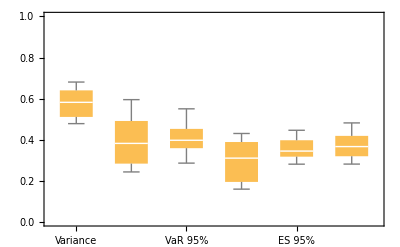

```mathematica
BoxWhiskerChart[Transpose[heInsample⟦1;;All,2;;All⟧],ChartLabels->methods,PlotRange->{0,1}]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample_box.png", %];
```

```mathematica
dates=Table[DateList[{heInsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heInsample⟦1;;All,1⟧]}];
```

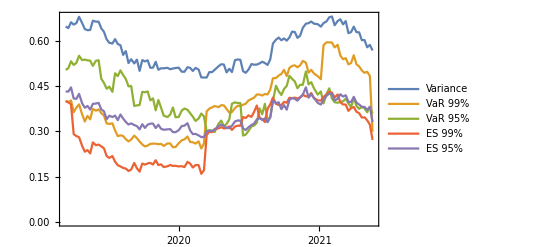

```mathematica
DateListPlot[Table[{dates,heInsample[[;;,k]]}ᵀ, {k,2,Dimensions[heInsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.png", %];
```

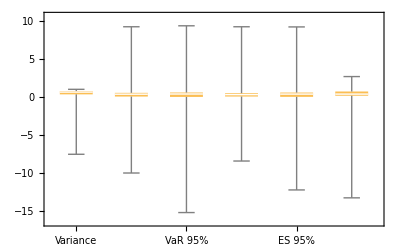

```mathematica
BoxWhiskerChart[heOutsample[[;;,2;;]]ᵀ, ChartLabels->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample_box.png", %];
```

```mathematica
dates=Table[DateList[{heOutsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heOutsample⟦1;;All,1⟧]}];
```

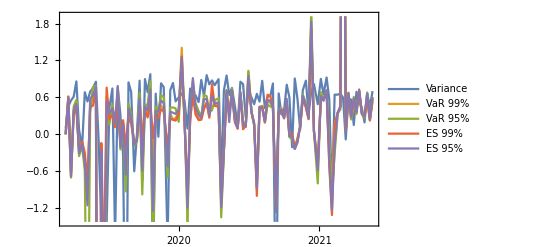

```mathematica
DateListPlot[Table[{dates,heOutsample[[;;,k]]}ᵀ, {k,2,Dimensions[heOutsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.png", %];
```

## P&L

```mathematica
data[[1,7]]
```

log return ltc

```mathematica
data[[1,6]]
```

log return future

```mathematica
data[[2,2]]
```

2019-03-11 20:00:00+00:00

### In-sample P&L

```mathematica
For[kk=0, kk≤111, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PL,PLbtc];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv",PLrᵀ]
]
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | ltc Price | log return future | log return ltc
560 | 2019-03-11 20:00:00+00:00 | 3835. | BTCJ19 Curncy | 54.3935 | -0.0142397 | -0.0619251
561 | 2019-03-08 21:00:00+00:00 | 3890. | BTCJ19 Curncy | 57.8683 | 0.00644748 | 0.0126448
562 | 2019-03-07 21:00:00+00:00 | 3865. | BTCJ19 Curncy | 57.1411 | 0.00648932 | 0.0520951
563 | 2019-03-06 21:00:00+00:00 | 3840. | BTCJ19 Curncy | 54.2406 | 0.00260756 | 0.0346593
564 | 2019-03-05 21:00:00+00:00 | 3830. | BTCJ19 Curncy | 52.3928 | 0.0358842 | 0.133181
565 | 2019-03-04 21:00:00+00:00 | 3695. | BTCJ19 Curncy | 45.8598 | -0.0332699 | -0.0549473
566 | 2019-03-01 21:00:00+00:00 | 3820. | BTCJ19 Curncy | 48.4502 | 0.0078844 | 0.0378498
567 | 2019-02-28 21:00:00+00:00 | 3790. | BTCH19 Curncy | 46.6506 | 0.0213341 | 0.0473755
568 | 2019-02-27 21:00:00+00:00 | 3710. | BTCH19 Curncy | 44.4921 | -0.0173685 | 0.000850901)

```mathematica
hvec
```

{{2019-03-11},{1.08957},{1.10891},{1.15707},{1.09752},{1.13276},{1.02959},{{0.09469694261283976, {h$490683576 -> 1.1089053103811357}},{0.057086630205371365, {h$490683576 -> 1.1570657807812303}},{0.11540802268027431, {h$490683576 -> 1.0975231998050474}},{0.08026431231322065, {h$490683576 -> 1.1327603434027467}},{0.06061801110152918, {h$490683576 -> 1.0295879516574036}}}}

### Out-of-sample P&L

```mathematica
For[kk=0, kk≤111, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv",PLrᵀ]
]
```

### Sandbox P&L in-sample

```mathematica
For[kk=0, kk≤111, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv",PLrᵀ]
]
```

### Sandbox P&L out-of-sample

```mathematica
For[kk=0, kk<=111, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,7⟧];
brr=Reverse[data⟦2;;All,6⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv",PLrᵀ]
]
```

## Plots

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

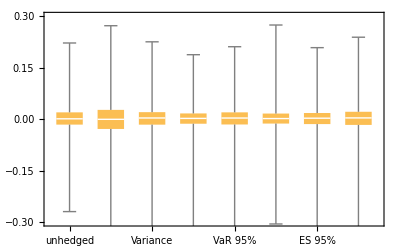

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

The overlap is clearly visible below.

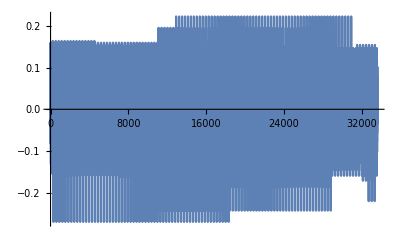

```mathematica
ListPlot[d[[2;;,2]], Joined->True,PlotRange->Full]
```

Out-of-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

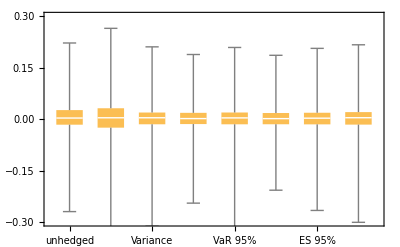

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

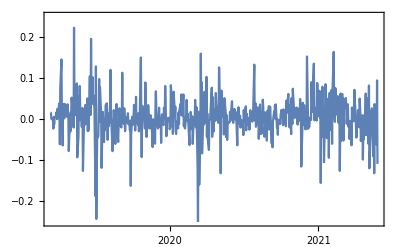
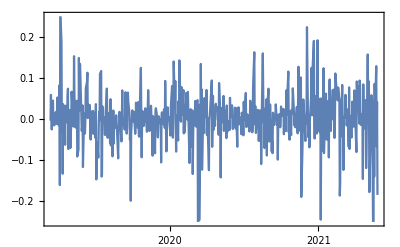

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25}], {m,2,3}]
```

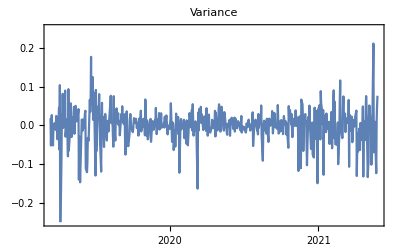
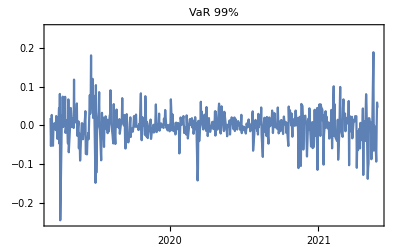
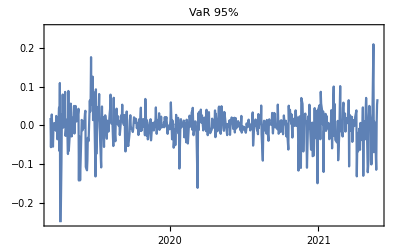
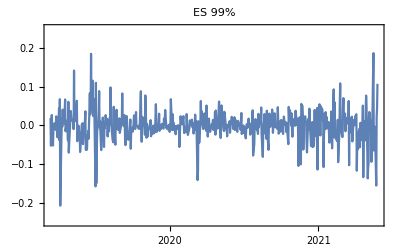
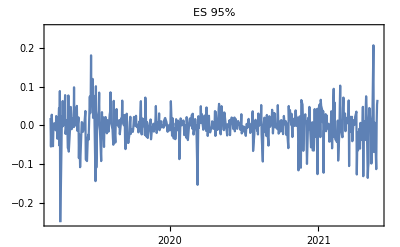
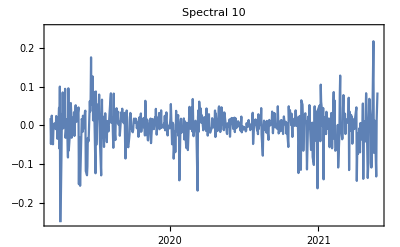

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods[[m-3]]], {m,4,9}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

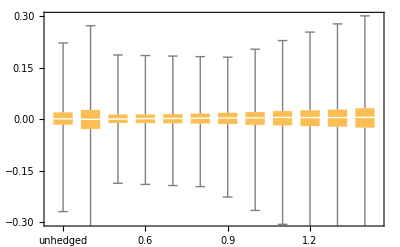

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=0, kk≤111, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

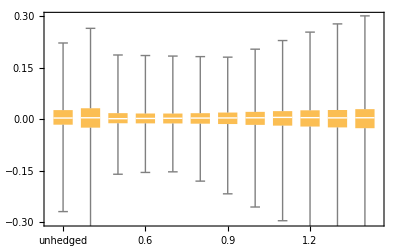

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

h time series

```mathematica
h={Join[{"Date"},methods]};
For[kk=0, kk≤111, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
dates=Table[DateList[{h⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[h⟦2;;All,1⟧]}];
```

```mathematica
h
```

(Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-05-20 | 1.08507 | 0.890404 | 1.0282 | 1.28632 | 1.01747 | 1.1392
2021-05-13 | 1.02673 | 0.939568 | 1.01963 | 0.930585 | 1.00928 | 1.0505
2021-05-06 | 1.01786 | 0.805643 | 1.01016 | 0.908084 | 0.975298 | 1.12933
2021-04-29 | 1.03732 | 1.05978 | 0.972512 | 1.05357 | 1.04753 | 1.0488
2021-04-22 | 1.04009 | 1.08665 | 0.994498 | 1.05219 | 1.03456 | 1.11075
2021-04-15 | 1.06227 | 1.02174 | 1.04287 | 1.07735 | 1.05343 | 1.12061
2021-04-08 | 1.0567 | 1.01403 | 1.05203 | 0.980805 | 1.02033 | 1.12243
2021-04-01 | 1.07522 | 0.880274 | 1.08366 | 0.9495 | 1.03944 | 1.18965
2021-03-25 | 1.06439 | 0.843512 | 1.04571 | 1.02008 | 1.00828 | 1.14988
2021-03-18 | 1.07202 | 1.02589 | 1.06742 | 0.963253 | 1.00744 | 1.1872
2021-03-11 | 1.09865 | 1.05369 | 1.08758 | 1.05358 | 1.07756 | 1.19268
2021-03-04 | 1.09216 | 1.05918 | 1.07366 | 1.05918 | 1.05663 | 1.17323
2021-02-25 | 1.10551 | 1.03484 | 0.957387 | 1.06433 | 1.07822 | 1.13729
2021-02-18 | 1.08859 | 0.959308 | 0.9755 | 1.03039 | 0.985402 | 1.18691
2021-02-10 | 1.07347 | 0.920989 | 0.983838 | 0.924627 | 0.967424 | 1.20951
2021-02-03 | 1.1177 | 0.962836 | 0.973125 | 1.08207 | 1.05936 | 1.18359
2021-01-27 | 1.11553 | 0.950783 | 0.973414 | 1.08329 | 1.05833 | 1.19273
2021-01-20 | 1.1107 | 0.947723 | 0.980136 | 0.929993 | 1.02379 | 1.20985
2021-01-12 | 1.10993 | 0.932696 | 1.0612 | 0.976024 | 1.07448 | 1.18791
2021-01-05 | 1.08847 | 0.918034 | 1.08011 | 0.896734 | 0.977213 | 1.17387
2020-12-28 | 1.07267 | 0.92973 | 1.07282 | 0.925756 | 0.975874 | 1.12572
2020-12-18 | 1.06889 | 0.945873 | 1.04529 | 0.93828 | 0.989274 | 1.15234
2020-12-11 | 1.06651 | 0.954763 | 1.0988 | 0.935644 | 0.994387 | 1.11271
2020-12-04 | 1.05851 | 0.947987 | 1.09557 | 0.933557 | 1.00599 | 1.08033
2020-11-27 | 1.04634 | 0.964258 | 1.06938 | 0.92537 | 1.03399 | 1.08501
2020-11-19 | 1.0314 | 0.962313 | 1.05671 | 0.962313 | 1.02417 | 1.02013
2020-11-12 | 0.993119 | 0.945027 | 0.987193 | 0.907766 | 0.983252 | 1.02849
2020-11-05 | 0.979088 | 0.936149 | 0.983663 | 0.895911 | 0.97887 | 0.983148
2020-10-29 | 0.998201 | 0.94423 | 0.991889 | 0.94395 | 0.994584 | 0.964785
2020-10-22 | 0.997349 | 0.941802 | 1.05237 | 0.935395 | 0.981051 | 0.966377
2020-10-15 | 0.974044 | 0.93736 | 1.00905 | 0.901224 | 0.981142 | 0.958085
2020-10-08 | 0.956776 | 0.899724 | 1.01942 | 0.867612 | 0.970223 | 0.92039
2020-10-01 | 0.962225 | 0.925382 | 1.00442 | 0.921965 | 0.968247 | 0.93124
2020-09-24 | 0.954807 | 0.908916 | 0.989942 | 0.976335 | 0.962945 | 0.924948
2020-09-17 | 0.973336 | 0.902595 | 0.985953 | 0.91085 | 0.97079 | 0.937854
2020-09-10 | 0.963276 | 0.900276 | 0.966043 | 0.86471 | 0.96274 | 0.931506
2020-09-02 | 0.880055 | 0.907267 | 0.784584 | 0.961422 | 0.945971 | 0.854513
2020-08-26 | 0.804221 | 0.860857 | 0.768275 | 1.05528 | 0.922872 | 0.738294
2020-08-19 | 0.783754 | 0.911143 | 0.785064 | 1.05377 | 0.91415 | 0.735899
2020-08-12 | 0.782206 | 0.730548 | 0.781238 | 0.72978 | 0.793642 | 0.713591
2020-08-05 | 0.783907 | 0.808251 | 0.76938 | 0.805274 | 0.877495 | 0.7309
2020-07-29 | 0.792461 | 0.812921 | 0.777208 | 0.74571 | 0.803475 | 0.770347
2020-07-22 | 0.789265 | 0.926647 | 0.777344 | 1.06626 | 0.934352 | 0.729247
2020-07-15 | 0.773672 | 0.811843 | 0.764555 | 0.995428 | 0.902975 | 0.747189
2020-07-08 | 0.776118 | 0.809513 | 0.781992 | 0.919194 | 0.884254 | 0.728312
2020-06-30 | 0.763415 | 0.799528 | 0.77109 | 0.983629 | 0.889356 | 0.716523
2020-06-23 | 0.757264 | 0.843404 | 0.763342 | 0.979476 | 0.8895 | 0.713835
2020-06-16 | 0.766615 | 0.836569 | 0.805661 | 0.991067 | 0.898311 | 0.720608
2020-06-09 | 0.83424 | 0.782938 | 0.917951 | 0.692068 | 0.811392 | 0.881341
2020-06-02 | 0.835872 | 0.786475 | 0.917951 | 0.692955 | 0.811725 | 0.881799
2020-05-26 | 0.833427 | 0.774449 | 0.791227 | 0.690963 | 0.802743 | 0.879076
2020-05-18 | 0.805257 | 0.686604 | 0.774379 | 0.67937 | 0.746187 | 0.86195
2020-05-11 | 0.824304 | 0.780944 | 0.803989 | 0.784321 | 0.864148 | 0.861404
2020-05-04 | 0.820156 | 0.77525 | 0.770057 | 0.690999 | 0.759989 | 0.875513
2020-04-27 | 0.852408 | 0.832521 | 0.919373 | 0.770791 | 0.839371 | 0.913702
2020-04-20 | 0.857164 | 0.78168 | 0.919748 | 0.69813 | 0.809926 | 0.906227
2020-04-13 | 0.870207 | 0.778699 | 0.916497 | 0.695911 | 0.808729 | 0.934908
2020-04-03 | 0.858938 | 0.779619 | 0.914838 | 0.769097 | 0.832364 | 0.867707
2020-03-27 | 0.858534 | 0.814061 | 0.914536 | 0.759426 | 0.82902 | 0.866196
2020-03-20 | 0.860711 | 0.776297 | 0.922139 | 0.712346 | 0.821158 | 0.901382
2020-03-13 | 0.862253 | 0.765888 | 0.913859 | 0.752885 | 0.850523 | 0.893415
2020-03-06 | 0.873414 | 0.492582 | 0.838411 | 0.473602 | 0.69753 | 0.965151
2020-02-28 | 0.875784 | 0.589316 | 0.83591 | 0.443731 | 0.702425 | 0.977457
2020-02-21 | 0.916198 | 0.5715 | 0.837762 | 0.513916 | 0.710378 | 1.03035
2020-02-13 | 0.920458 | 0.672076 | 0.854185 | 0.542795 | 0.729772 | 1.08781
2020-02-06 | 0.905792 | 0.562978 | 0.859018 | 0.474381 | 0.682824 | 1.06669
2020-01-30 | 0.893557 | 0.51228 | 0.831618 | 0.516003 | 0.668449 | 0.997229
2020-01-23 | 0.888091 | 0.594228 | 0.825869 | 0.492228 | 0.682795 | 1.00006
2020-01-15 | 0.872854 | 0.560319 | 0.82917 | 0.449969 | 0.678593 | 0.970923
2020-01-08 | 0.866923 | 0.555874 | 0.829611 | 0.467179 | 0.676836 | 1.0043
2019-12-31 | 0.88162 | 0.536713 | 0.804768 | 0.522447 | 0.698781 | 0.951043
2019-12-23 | 0.881342 | 0.533703 | 0.837226 | 0.44229 | 0.659792 | 0.978173
2019-12-16 | 0.882613 | 0.446253 | 0.824563 | 0.446253 | 0.663564 | 0.991115
2019-12-09 | 0.879371 | 0.612052 | 0.790177 | 0.469686 | 0.668016 | 0.957585
2019-12-02 | 0.888939 | 0.570023 | 0.804525 | 0.52893 | 0.702466 | 0.973534
2019-11-22 | 0.894887 | 0.543887 | 0.844191 | 0.519344 | 0.703622 | 0.988108
2019-11-15 | 0.901161 | 0.609711 | 0.828413 | 0.527194 | 0.717558 | 0.966052
2019-11-08 | 0.90049 | 0.683001 | 0.791692 | 0.482928 | 0.712417 | 0.998022
2019-11-01 | 0.924371 | 0.789932 | 0.928652 | 0.619421 | 0.775985 | 1.00031
2019-10-25 | 0.912846 | 0.568949 | 0.853311 | 0.490074 | 0.713078 | 1.043
2019-10-18 | 0.928267 | 0.569324 | 0.866182 | 0.52548 | 0.732625 | 0.982924
2019-10-11 | 0.948199 | 0.615902 | 0.913756 | 0.523925 | 0.756725 | 1.01992
2019-10-04 | 0.944673 | 0.672159 | 0.971648 | 0.510561 | 0.750859 | 0.979392
2019-09-27 | 0.946446 | 0.633602 | 0.820093 | 0.530276 | 0.75742 | 1.01313
2019-09-20 | 0.912841 | 0.667002 | 0.823805 | 0.506436 | 0.709017 | 0.994862
2019-09-13 | 0.941978 | 0.726092 | 0.930298 | 0.57587 | 0.757867 | 1.00697
2019-09-06 | 0.93242 | 0.715791 | 0.820124 | 0.594493 | 0.736409 | 1.06882
2019-08-29 | 0.951738 | 0.645361 | 0.892027 | 0.462995 | 0.73865 | 1.04268
2019-08-22 | 0.939398 | 0.578694 | 0.851727 | 0.463676 | 0.721856 | 0.984112
2019-08-15 | 0.976107 | 0.562496 | 0.888292 | 0.47164 | 0.733429 | 1.03499
2019-08-08 | 0.967109 | 0.588408 | 0.889204 | 0.460238 | 0.74218 | 1.09161
2019-08-01 | 1.00092 | 0.65491 | 0.900654 | 0.492706 | 0.771152 | 1.10917
2019-07-25 | 1.00349 | 0.657877 | 0.948155 | 0.471614 | 0.77135 | 1.05808
2019-07-18 | 1.02226 | 0.633112 | 0.927811 | 0.513539 | 0.796177 | 1.07292
2019-07-11 | 1.00103 | 0.788809 | 0.922928 | 0.592042 | 0.803192 | 1.06932
2019-07-03 | 1.00634 | 0.707427 | 0.992455 | 0.5543 | 0.776404 | 1.0749
2019-06-26 | 1.10421 | 0.736293 | 1.05832 | 0.561139 | 0.822296 | 1.22057
2019-06-19 | 1.16964 | 0.924041 | 1.21144 | 0.680272 | 0.918333 | 1.24175
2019-06-12 | 1.19023 | 0.815083 | 1.25088 | 0.678147 | 0.930923 | 1.29992
2019-06-05 | 1.20152 | 0.761179 | 1.15599 | 0.641558 | 0.930167 | 1.27548
2019-05-29 | 1.21237 | 0.755656 | 1.17709 | 0.645764 | 0.926326 | 1.30524
2019-05-21 | 1.20028 | 0.852489 | 1.16945 | 0.709764 | 0.960757 | 1.25441
2019-05-14 | 1.17043 | 0.714805 | 1.18215 | 0.557911 | 0.861062 | 1.23393
2019-05-07 | 1.20745 | 0.747732 | 1.19468 | 0.586876 | 0.88157 | 1.29658
2019-04-30 | 1.20901 | 0.836998 | 1.18863 | 0.599999 | 0.922043 | 1.23545
2019-04-23 | 1.22724 | 0.821085 | 1.15599 | 0.723864 | 0.976128 | 1.26294
2019-04-15 | 1.24097 | 0.953565 | 1.18151 | 0.831617 | 1.03148 | 1.32554
2019-04-08 | 1.18004 | 1.11605 | 1.16384 | 0.831308 | 1.0188 | 1.2113
2019-04-01 | 1.13885 | 0.970981 | 1.18057 | 0.871829 | 1.02539 | 1.11137
2019-03-25 | 1.125 | 1.10629 | 1.12601 | 1.03419 | 1.10077 | 1.10304
2019-03-18 | 1.09654 | 1.12768 | 1.2099 | 1.09653 | 1.15538 | 0.980418
2019-03-11 | 1.08957 | 1.10891 | 1.15707 | 1.09752 | 1.13276 | 1.02959)

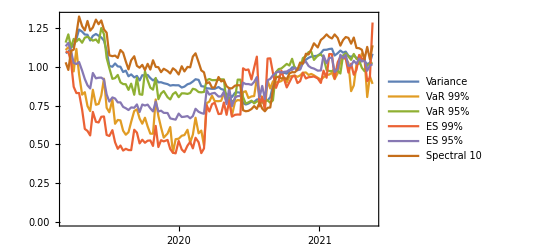

```mathematica
DateListPlot[Table[{dates,h[[2;;,k+1]]}ᵀ, {k,1,Dimensions[h][[2]]-1}],PlotLegends->methods,PlotRange->Full]
```